## Project Notes

### hist

```mathematica
h=With[{min=Min[#[[All,1,2]],#[[1,1,2]]-11]-1},
Transpose[{
#-{0,min,0}&/@#[[All,1]],
ArrayPad[
#[[All,2]],
{{0,0},{-min,#[[1,1,2]]-Length[#[[1,2]]]-#[[1,1,3]]}}
]
}]
]&@
Module[{halt=False},
TakeWhile[
#,
Which[
halt,
False,
-10<=#[[1,3]]<=0,
True,
MatchQ[#[[1,3]],1|-11],
halt=True
]&
]
]&@
TuringMachine[2237,{{1,11},{IntegerDigits[10,2,11],0}},100];
%//Column
```

{{1,12,0},{0,0,0,0,0,0,0,0,1,0,1,0}}
{{1,11,-1},{0,0,0,0,0,0,0,0,1,0,1,1}}
{{2,10,-2},{0,0,0,0,0,0,0,0,1,0,0,1}}
{{2,11,-1},{0,0,0,0,0,0,0,0,1,0,0,1}}
{{2,12,0},{0,0,0,0,0,0,0,0,1,0,0,1}}
{{2,13,1},{0,0,0,0,0,0,0,0,1,0,0,1}}

```mathematica
res=Module[{halt=False},
TakeWhile[
#,
Which[
halt,
False,
-10<=#[[1,3]]<=0,(* offsets in [-10,0], positions from 1 to 11 *)
True,
MatchQ[#[[1,3]],1|-11], (* halt offsets: position 12 or 0 *)
halt=True
]&
]
]&@
TuringMachine[3279,{{1,11},{IntegerDigits[10,2,11],0}},3]

res[[All,1,2]] ;(* positions *)
res[[1,1,2]]-11; (* initial position - 11 *)
min=Min[%%,%]-1
```

{{{1,11,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0}},{{1,12,1},{0,0,0,0,0,0,0,1,0,1,1,0,0,0}}}

-1

```mathematica
#-{0,min,0}&/@res[[All,1]]
```

{{1,12,0},{1,13,1}}

```mathematica
res[[All,2]]
res[[1]]
#[[1,1,2]]-Length[#[[1,2]]]-#[[1,1,3]]&@res
ArrayPad[
#[[All,2]],
{{0,0},{-min,#[[1,1,2]]-Length[#[[1,2]]]-#[[1,1,3]]}}
]&@res
```

{{0,0,0,0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,1,0,0,0}}

{{1,11,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0}}

-3

{{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,0,1,1}}

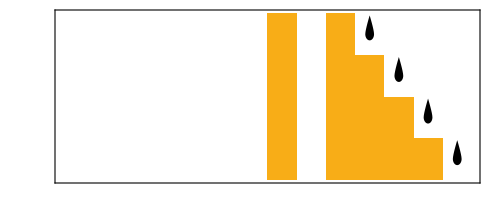

```mathematica
RulePlot[TuringMachine[3279],{{1,11},{IntegerDigits[10,2,11],0}},3]
```

### Show Plot

```mathematica
Show[{
RulePlot[
TuringMachine[445],
h,
Sequence[
Mesh->True,
MeshStyle->Directive[Thin,GrayLevel[0.15]],
ImageSize->{50,Automatic},
Frame->False
]
],
Graphics[{ (* gray boxes at the end *)
GrayLevel[.85],
EdgeForm[{Thin,GrayLevel[.15]}],
Table[Rectangle[{Length[h[[1,2]]],y}],{y,0,Length[h]-1}],
If[ (* does not halt after 100 iterations *)
h[[-1,1,3]]!=1,
{
Black,
Translate[
Triangle[{{-1,0},{1,0},{0,-1.5}}],
{Length[h[[1,2]]]/2,-1}
]
},
{}
] (* end If *)
}] (* end Graphics *)
}] (* end Show *)
```

-Graphics-

### Halting Time With Init

```mathematica
ht=Table[
Module[{t=0,max=50+2^(Log[2,n]+1)},
NestWhile[
(t++;TuringMachine[3279,#])&,
{{1,9,0},{IntegerDigits[n,2,9],0}},
#[[1,3]]<=0&,(* stop when dx > 0, or when x >= 10 *)
1,
max
];
If[t==max,0,t]
],
{n,0,511}
]
```

{1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5,1,3,1,5}

### ht graphics

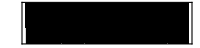

```mathematica
Graphics[{
{
GrayLevel[0.85],
Table[
Rectangle[
{2^(i-1),-Max[Take[ht,{2^(i-1)+1,2^i}]]},
{2^i,0}
],
{i,9}
]
},{
MapIndexed[Rectangle[{Last[#2],0},{Last[#2]+1,-#1}]&,ht]
}
},
Sequence[
PlotRangePadding->{5,{Scaled[0.1],Scaled[0.05]}},
Frame->True,
FrameTicks->False,AspectRatio->2 (Log[Max[ht]]/(3 Log[Length[ht]])),
ImageSize->{200,Automatic}
]
]
```

### Complete

```mathematica
start=5*12^4;
r=Range[start-2,start+1]
states=3;
colors=2;
```

{103678,103679,103680,103681}

```mathematica
Grid[
ParallelTable[
Flatten@{
RulePlot[TuringMachine[{rule,states,colors}],ImageSize->300],
Table[
With[{ (* With init *)
hist=With[{min=Min[#[[All,1,2]],#[[1,1,2]]-11]-1},
Transpose[{
#-{0,min,0}&/@#[[All,1]],
ArrayPad[
#[[All,2]],
{{0,0},{-min,#[[1,1,2]]-Length[#[[1,2]]]-#[[1,1,3]]}}
]
}]
]&@
Module[{halt=False},
TakeWhile[
#,
Which[
halt,
False,
-10<=#[[1,3]]<=0,(* valid position *)
True,
MatchQ[#[[1,3]],1|-11], (* halt position *)
halt=True
]&
]
]&@
TuringMachine[{rule,states,colors},{{1,11},{IntegerDigits[n,2,11],0}},100]
},(* end With init *)
Show[{
RulePlot[
TuringMachine[{rule,states,colors}],
hist,
Sequence[
Mesh->True,
MeshStyle->Directive[Thin,GrayLevel[0.15]],
ImageSize->{200,Automatic},
Frame->False
]
],
Graphics[{
GrayLevel[.85],
EdgeForm[{Thin,GrayLevel[.15]}],
Table[Rectangle[{Length[hist[[1,2]]],y}],{y,0,Length[hist]-1}],
If[
hist[[-1,1,3]]!=1,
{
Black,
Translate[
Triangle[{{-1,0},{1,0},{0,-1.5}}],
{Length[hist[[1,2]]]/2,-1}
]
},
{}
] (* end If *)
}] (* end Graphics *)
}] (* end Show *)
],(* end With *)
{n,1,20}
], (* end Table *)
With[{
haltingTimes=Table[
Module[{t=0,max=50+2^(Log[2,n]+1)},
NestWhile[
(t++;TuringMachine[{rule,states,colors},#])&,
{{1,9,0},{IntegerDigits[n,2,9],0}},
-10<=#[[1,3]]<=0&,
1,
max
];
If[t==max,0,t]
],
{n,0,511}
]
},(* end With init*)
Graphics[{
{
GrayLevel[0.85],
Table[
Rectangle[
{2^(i-1),-Max[Take[haltingTimes,{2^(i-1)+1,2^i}]]},
{2^i,0}
],
{i,9}
]
},{
MapIndexed[Rectangle[{Last[#2],0},{Last[#2]+1,-#1}]&,haltingTimes]
}
},
Sequence[
PlotRangePadding->{5,{Scaled[0.1],Scaled[0.05]}},
Frame->True,
FrameTicks->False,AspectRatio->2 (Log[Max[haltingTimes]]/(3 Log[Length[haltingTimes]])),
ImageSize->{300,Automatic}
]
] (* end Graphics *)
] (* end With *)
},(* end Flatten *)
{rule,r}
], (* end Table *)
Sequence[
Alignment->Top,
Dividers->{True,{True,True,False,False,True,True,False,False,True,False,True,True}}
]
](* end Grid *)
```

```mathematica
timeof[n_,k_]:=(2n*k)^(n*k)-k(k+1)(2n*k)^(n*k-2)
timeof[n,k]//FullSimplify
```

2^(-2+k n) k (k n)^(-2+k n) (-1+k (-1+4 n^2))

0 to 12^4 returns 0

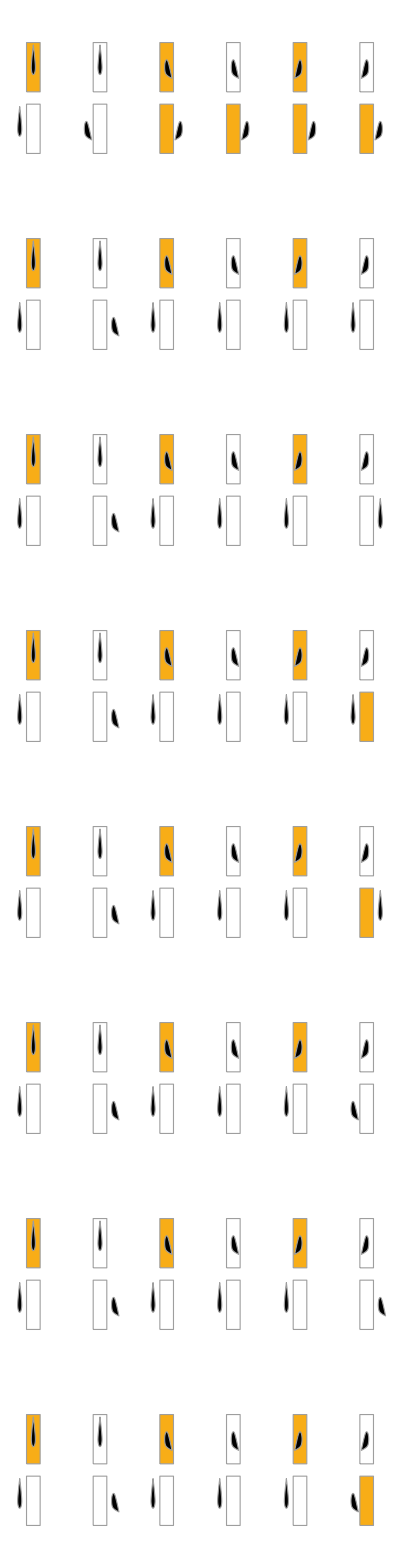

```mathematica
RulePlot[TuringMachine[{#,states,colors}],ImageSize->Large]&/@r//Column
```

```mathematica
ResourceFunction["TuringMachineFromNumber"][#,states,colors]&/@r//Column
```

{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{1,0,-1}}
{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{1,0,1}}
{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{1,1,-1}}
{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{1,1,1}}
{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{2,0,-1}}
{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{2,0,1}}
{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{2,1,-1}}
{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{2,1,1}}
{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,1},{2,0}→{1,0,-1}}

## TM

```mathematica
rules={
{1,1}->{2,0,1},
{1,0}->{3,1,-1},
{2,1}->{3,1,1},
{2,0}->{1,1,1},
{3,1}->{1,0,-1},
{3,0}->{2,1,1}
};
init={1,{{},0}};
```

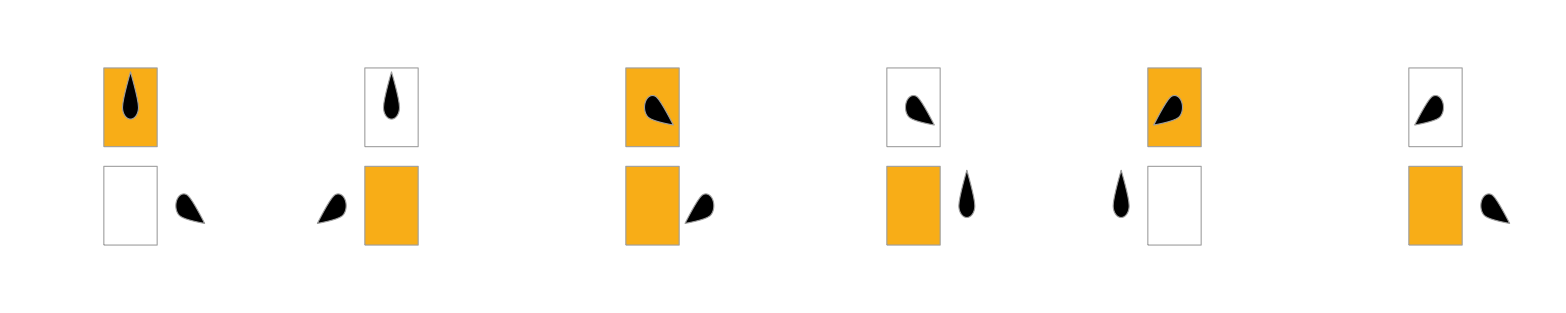

```mathematica
RulePlot[TuringMachine[rules]]
```

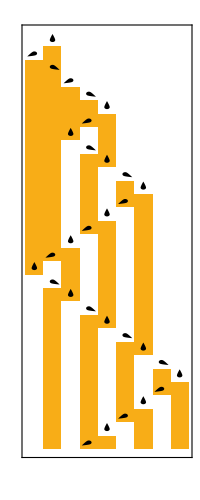

```mathematica
RulePlot[TuringMachine[rules],init,30]
```

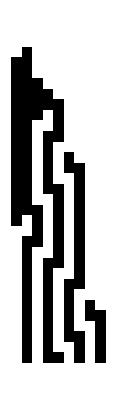

```mathematica
ArrayPlot[Last/@TuringMachine[rules,init,30]]
```